```mathematica
Mx=10;
My=20;
```

```mathematica
Δx=1./Mx; Δy=1./My;
```

```mathematica
Clear[ϕ]
```

```mathematica
ϕ[0,k_,n_]= 0;
ϕ[Mx,k_,n_]=0;
ϕ[j_,0,n_]=0;
ϕ[j_,My,n_]=0;
```

```mathematica
ϕ[j_,k_,0]=0;
```

```mathematica
ϕ[j_,k_,n_]:= ϕ[j,k,n]=Δt((ϕ[j+1,k,n-1]+ϕ[j-1,k,n-1])/Δx^2+(ϕ[j,k+1,n-1]+ϕ[j,k-1,n-1])/Δy^2- j Δx)
```

```mathematica
Δt=Δx^2 Δy^2/(2(Δx^2+Δy^2))
```

0.001

```mathematica
error[n_]:= Max[Table[ϕ[j,k,n]-ϕ[j,k,n-1]//Abs,{j,1,Mx-1},{k,1,My-1}]]
```

```mathematica
error[1]
```

0.0009

```mathematica
error[2]
```

0.0008

```mathematica
error[3]
```

0.00079

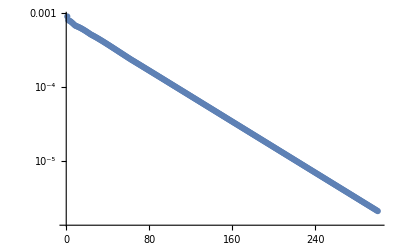

```mathematica
Table[error[n],{n,1,300}]//ListLogPlot
```

```mathematica
ϕtab=Table[{j Δx, k Δy, ϕ[j,k,300]},{j,0,Mx},{k,0,My}];
```

```mathematica
ϕs=Interpolation[Flatten[ϕtab,1]]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

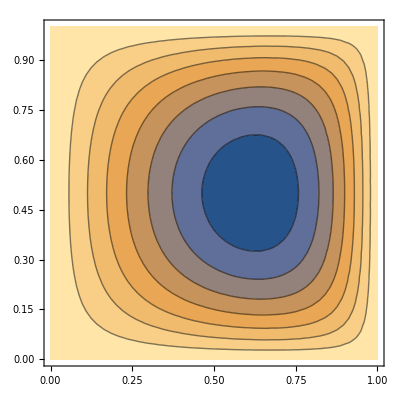

```mathematica
ContourPlot[ϕs[x,y],{x,0,1},{y,0,1}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
Mx=10;
My=20;
```

```mathematica
Δx=1./Mx; Δy=1./My;
```

```mathematica
Clear[ϕ]
```

```mathematica
ϕ[0,k_,n_]= 0;
ϕ[Mx,k_,n_]=0;
ϕ[j_,0,n_]=0;
ϕ[j_,My,n_]=0;
```

```mathematica
ϕ[j_,k_,0]=0;
```

```mathematica
ϕ[j_,k_,n_]:= ϕ[j,k,n]=(1-ω)ϕ[j,k,n-1]+ω Δt((ϕ[j+1,k,n-1]+ϕ[j-1,k,n])/Δx^2+(ϕ[j,k+1,n-1]+ϕ[j,k-1,n])/Δy^2- j Δx)
```

```mathematica
Δt=Δx^2 Δy^2/(2(Δx^2+Δy^2))
```

0.001

```mathematica
ω=1.7;
```

```mathematica
error[n_]:= Max[Table[ϕ[j,k,n]-ϕ[j,k,n-1]//Abs,{j,1,Mx-1},{k,1,My-1}]]
```

```mathematica
error[1]
```

0.00881425

```mathematica
error[2]
```

0.00759677

```mathematica
error[3]
```

0.00640336

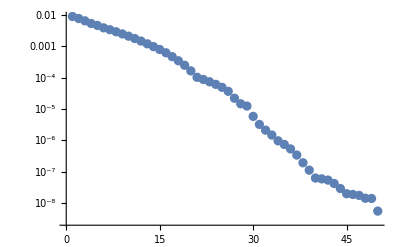

```mathematica
Table[error[n],{n,1,50}]//ListLogPlot
```

```mathematica
ϕtab=Table[{j Δx, k Δy, ϕ[j,k,50]},{j,0,Mx},{k,0,My}];
```

```mathematica
ϕs=Interpolation[Flatten[ϕtab,1]]
```

InterpolatingFunction[{{0., 1.}, {0., 1.}}, <>]

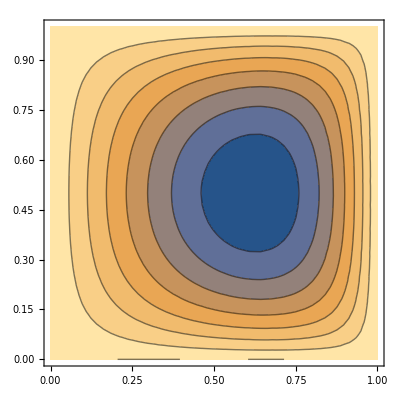

```mathematica
ContourPlot[ϕs[x,y],{x,0,1},{y,0,1}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
M=20;
```

```mathematica
Δx = Δy = 1./M
```

0.05

```mathematica
x[j_]= j Δx; y[k_]= k Δy;
```

```mathematica
xmax[y_]= Sqrt[3] -y (Sqrt[3]-1)
```

√3-(-1+√3) y

```mathematica
g[k_]= Floor[xmax[y[k]]/Δx];
```

```mathematica
points=Table[Table[{x[j],y[k]},{j,k,g[k]+1}],{k,0,M}];
```

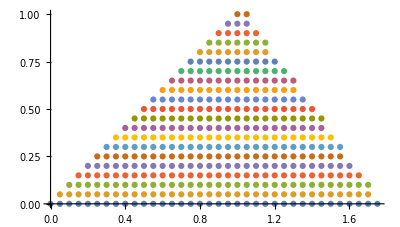

```mathematica
ListPlot[points,AspectRatio->Automatic]
```

```mathematica
Plot[(Sqrt[3]-x)/(Sqrt[3]-1),{x,1,Sqrt[3]}];
```

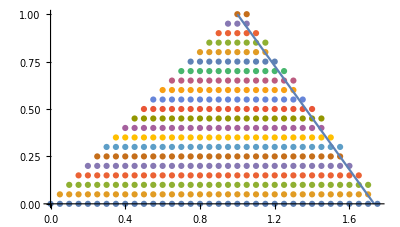

```mathematica
Show[%%,%]
```

```mathematica
ϕ[j_,0]=0;
```

```mathematica
ϕ[j_,j_]= 0;
```

```mathematica
Δx1[k_]= xmax[y[k]]-x[g[k]];
```

```mathematica
Δx2[k_]= Δx - Δx1[k];
```

```mathematica
ϕ[j_,k_]:= - Δx2[k]/Δx1[k] ϕ[j-1,k]/; j==g[k]+1 && k<M
```

```mathematica
eqns=Table[Table[(ϕ[j+1,k]-2ϕ[j,k]+ϕ[j-1,k])/Δx^2+(ϕ[j,k+1]-2ϕ[j,k]+ϕ[j,k-1])/Δy^2-x[j]==0,{j,k+1,g[k]}],{k,1,M-1}]//Flatten;
```

```mathematica
Length[eqns]
```

319

```mathematica
g[10]
```

27

```mathematica
vars=Table[Table[ϕ[j,k],{j,k+1,g[k]}],{k,1,M-1}]//Flatten;
```

```mathematica
Length[vars]
```

319

```mathematica
sl=Solve[eqns,vars]
```

{{ϕ[2,1]→-0.000201633,ϕ[3,1]→-0.000556532,ϕ[4,1]→-0.00104758,ϕ[5,1]→-0.00165767,ϕ[6,1]→-0.00236969,ϕ[7,1]→-0.00316656,ϕ[8,1]→-0.00403124,ϕ[9,1]→-0.00494673,ϕ[10,1]→-0.00589612,ϕ[11,1]→-0.0068626,ϕ[12,1]→-0.00782953,ϕ[13,1]→-0.00878048,ϕ[14,1]→-0.00969924,ϕ[15,1]→-0.0105699,ϕ[16,1]→-0.011377,ϕ[17,1]→-0.0121054,ϕ[18,1]→-0.0127405,ϕ[19,1]→-0.0132681,ϕ[20,1]→-0.0136745,ϕ[21,1]→-0.0139468,ϕ[22,1]→-0.0140723,ϕ[23,1]→-0.0140389,ϕ[24,1]→-0.0138348,ϕ[25,1]→-0.0134485,ϕ[26,1]→-0.0128688,ϕ[27,1]→-0.0120842,ϕ[28,1]→-0.0110834,ϕ[29,1]→-0.00985429,ϕ[30,1]→-0.00838444,ϕ[31,1]→-0.00666001,ϕ[32,1]→-0.00466417,ϕ[33,1]→-0.00237394,ϕ[3,2]→-0.000601914,ϕ[4,2]→-0.00147612,ϕ[5,2]→-0.0025884,ϕ[6,2]→-0.00390452,ϕ[7,2]→-0.00539032,ϕ[8,2]→-0.00701167,ϕ[9,2]→-0.00873456,ϕ[10,2]→-0.0105251,ϕ[11,2]→-0.0123497,ϕ[12,2]→-0.0141751,ϕ[13,2]→-0.0159681,ϕ[14,2]→-0.0176965,ϕ[15,2]→-0.0193285,ϕ[16,2]→-0.0208328,ϕ[17,2]→-0.0221792,ϕ[18,2]→-0.0233385,ϕ[19,2]→-0.0242822,ϕ[20,2]→-0.0249833,ϕ[21,2]→-0.0254154,ϕ[22,2]→-0.0255536,ϕ[23,2]→-0.0253734,ϕ[24,2]→-0.0248517,ϕ[25,2]→-0.0239655,ϕ[26,2]→-0.0226924,ϕ[27,2]→-0.0210098,ϕ[28,2]→-0.018895,ϕ[29,2]→-0.0163244,ϕ[30,2]→-0.0132735,ϕ[31,2]→-0.00971643,ϕ[32,2]→-0.00562274,ϕ[33,2]→-0.000944342,ϕ[4,3]→-0.0011666,ϕ[5,3]→-0.00269028,ϕ[6,3]→-0.00451969,ϕ[7,3]→-0.00660353,ϕ[8,3]→-0.00889056,ϕ[9,3]→-0.0113297,ϕ[10,3]→-0.0138701,ϕ[11,3]→-0.0164612,ϕ[12,3]→-0.0190528,ϕ[13,3]→-0.0215955,ϕ[14,3]→-0.0240404,ϕ[15,3]→-0.0263396,ϕ[16,3]→-0.0284463,ϕ[17,3]→-0.0303152,ϕ[18,3]→-0.0319019,ϕ[19,3]→-0.0331641,ϕ[20,3]→-0.0340609,ϕ[21,3]→-0.0345531,ϕ[22,3]→-0.034603,ϕ[23,3]→-0.0341746,ϕ[24,3]→-0.0332331,ϕ[25,3]→-0.0317444,ϕ[26,3]→-0.0296754,ϕ[27,3]→-0.0269927,ϕ[28,3]→-0.0236624,ϕ[29,3]→-0.0196497,ϕ[30,3]→-0.0149186,ϕ[31,3]→-0.00943452,ϕ[32,3]→-0.00316602,ϕ[5,4]→-0.00186143,ϕ[6,4]→-0.00413043,ϕ[7,4]→-0.00673853,ϕ[8,4]→-0.00961734,ϕ[9,4]→-0.0126986,ϕ[10,4]→-0.0159144,ϕ[11,4]→-0.0191971,ϕ[12,4]→-0.0224796,ϕ[13,4]→-0.0256956,ϕ[14,4]→-0.0287798,ϕ[15,4]→-0.0316682,ϕ[16,4]→-0.0342979,ϕ[17,4]→-0.0366081,ϕ[18,4]→-0.0385399,ϕ[19,4]→-0.0400365,ϕ[20,4]→-0.0410432,ϕ[21,4]→-0.0415079,ϕ[22,4]→-0.0413808,ϕ[23,4]→-0.040614,ϕ[24,4]→-0.0391615,ϕ[25,4]→-0.0369787,ϕ[26,4]→-0.0340221,ϕ[27,4]→-0.0302481,ϕ[28,4]→-0.0256123,ϕ[29,4]→-0.0200683,ϕ[30,4]→-0.0135667,ϕ[31,4]→-0.00606204,ϕ[6,5]→-0.00265206,ϕ[7,5]→-0.00572782,ϕ[8,5]→-0.00914165,ϕ[9,5]→-0.0128081,ϕ[10,5]→-0.0166418,ϕ[11,5]→-0.0205581,ϕ[12,5]→-0.0244728,ϕ[13,5]→-0.0283025,ϕ[14,5]→-0.0319652,ϕ[15,5]→-0.0353803,ϕ[16,5]→-0.0384689,ϕ[17,5]→-0.0411546,ϕ[18,5]→-0.0433632,ϕ[19,5]→-0.0450236,ϕ[20,5]→-0.0460674,ϕ[21,5]→-0.0464297,ϕ[22,5]→-0.0460483,ϕ[23,5]→-0.044864,ϕ[24,5]→-0.0428201,ϕ[25,5]→-0.039862,ϕ[26,5]→-0.0359362,ϕ[27,5]→-0.0309902,ϕ[28,5]→-0.0249704,ϕ[29,5]→-0.0178197,ϕ[30,5]→-0.00946785,ϕ[7,6]→-0.00350405,ϕ[8,6]→-0.00741339,ϕ[9,6]→-0.0116251,ϕ[10,6]→-0.0160367,ϕ[11,6]→-0.0205458,ϕ[12,6]→-0.0250509,ϕ[13,6]→-0.0294515,ϕ[14,6]→-0.0336483,ϕ[15,6]→-0.0375439,ϕ[16,6]→-0.041043,ϕ[17,6]→-0.0440531,ϕ[18,6]→-0.0464848,ϕ[19,6]→-0.0482522,ϕ[20,6]→-0.0492733,ϕ[21,6]→-0.0494701,ϕ[22,6]→-0.0487687,ϕ[23,6]→-0.0470986,ϕ[24,6]→-0.0443931,ϕ[25,6]→-0.0405878,ϕ[26,6]→-0.0356206,ϕ[27,6]→-0.0294309,ϕ[28,6]→-0.0219596,ϕ[29,6]→-0.013147,ϕ[30,6]→-0.00292077,ϕ[8,7]→-0.0043827,ϕ[9,7]→-0.00911743,ϕ[10,7]→-0.014084,ϕ[11,7]→-0.0191624,ϕ[12,7]→-0.0242335,ϕ[13,7]→-0.0291792,ϕ[14,7]→-0.0338826,ϕ[15,7]→-0.0382289,ϕ[16,7]→-0.042106,ϕ[17,7]→-0.045405,ϕ[18,7]→-0.0480206,ϕ[19,7]→-0.049852,ϕ[20,7]→-0.0508034,ϕ[21,7]→-0.0507839,ϕ[22,7]→-0.0497076,ϕ[23,7]→-0.0474938,ϕ[24,7]→-0.0440658,ϕ[25,7]→-0.0393505,ϕ[26,7]→-0.0332774,ϕ[27,7]→-0.0257783,ϕ[28,7]→-0.0167902,ϕ[29,7]→-0.00626285,ϕ[9,8]→-0.00525294,ϕ[10,8]→-0.0107693,ϕ[11,8]→-0.0164113,ϕ[12,8]→-0.0220417,ϕ[13,8]→-0.0275241,ϕ[14,8]→-0.0327238,ϕ[15,8]→-0.0375082,ϕ[16,8]→-0.0417473,ϕ[17,8]→-0.0453153,ϕ[18,8]→-0.0480905,ϕ[19,8]→-0.049957,ϕ[20,8]→-0.0508045,ϕ[21,8]→-0.0505293,ϕ[22,8]→-0.0490341,ϕ[23,8]→-0.0462281,ϕ[24,8]→-0.0420258,ϕ[25,8]→-0.0363461,ϕ[26,8]→-0.0291103,ϕ[27,8]→-0.0202397,ϕ[28,8]→-0.00966009,ϕ[10,9]→-0.00607906,ϕ[11,9]→-0.0122969,ϕ[12,9]→-0.0184978,ϕ[13,9]→-0.0245269,ϕ[14,9]→-0.0302305,ϕ[15,9]→-0.0354575,ϕ[16,9]→-0.0400598,ϕ[17,9]→-0.0438932,ϕ[18,9]→-0.0468193,ϕ[19,9]→-0.0487059,ϕ[20,9]→-0.0494282,ϕ[21,9]→-0.0488696,ϕ[22,9]→-0.0469215,ϕ[23,9]→-0.0434838,ϕ[24,9]→-0.0384632,ϕ[25,9]→-0.0317728,ϕ[26,9]→-0.0233278,ϕ[27,9]→-0.0130352,ϕ[28,9]→-0.000762317,ϕ[11,10]→-0.00682443,ϕ[12,10]→-0.0136258,ϕ[13,10]→-0.0202299,ϕ[14,10]→-0.0264639,ϕ[15,10]→-0.0321567,ϕ[16,10]→-0.037141,ϕ[17,10]→-0.0412535,ϕ[18,10]→-0.0443376,ϕ[19,10]→-0.0462441,ϕ[20,10]→-0.046833,ϕ[21,10]→-0.0459743,ϕ[22,10]→-0.0435487,ϕ[23,10]→-0.0394472,ϕ[24,10]→-0.0335705,ϕ[25,10]→-0.025829,ϕ[26,10]→-0.0161429,ϕ[27,10]→-0.00443587,ϕ[12,11]→-0.00745101,ϕ[13,11]→-0.0146782,ϕ[14,11]→-0.0214883,ϕ[15,11]→-0.0276896,ϕ[16,11]→-0.0330938,ϕ[17,11]→-0.0375173,ϕ[18,11]→-0.0407835,ϕ[19,11]→-0.042725,ϕ[20,11]→-0.0431852,ϕ[21,11]→-0.0420208,ϕ[22,11]→-0.0391017,ϕ[23,11]→-0.0343108,ϕ[24,11]→-0.0275426,ϕ[25,11]→-0.0187049,ϕ[26,11]→-0.00772904,ϕ[13,12]→-0.00791866,ϕ[14,12]→-0.0153714,ϕ[15,12]→-0.0221446,ϕ[16,12]→-0.0280273,ϕ[17,12]→-0.0328134,ϕ[18,12]→-0.0363042,ϕ[19,12]→-0.0383119,ϕ[20,12]→-0.0386622,ϕ[21,12]→-0.0371972,ϕ[22,12]→-0.0337766,ϕ[23,12]→-0.0282765,ϕ[24,12]→-0.0205844,ϕ[25,12]→-0.0105938,ϕ[14,13]→-0.00818415,ϕ[15,13]→-0.0156152,ϕ[16,13]→-0.0220574,ϕ[17,13]→-0.0272796,ϕ[18,13]→-0.0310581,ϕ[19,13]→-0.0331814,ϕ[20,13]→-0.0334545,ϕ[21,13]→-0.031704,ϕ[22,13]→-0.0277809,ϕ[23,13]→-0.0215592,ϕ[24,13]→-0.0129248,ϕ[25,13]→-0.00173707,ϕ[15,14]→-0.00819945,ϕ[16,14]→-0.0153076,ϕ[17,14]→-0.0210645,ϕ[18,14]→-0.0252173,ϕ[19,14]→-0.0275259,ϕ[20,14]→-0.0277703,ϕ[21,14]→-0.0257585,ϕ[22,14]→-0.0213338,ϕ[23,14]→-0.0143798,ϕ[24,14]→-0.00481834,ϕ[16,15]→-0.00790906,ϕ[17,15]→-0.0143286,ϕ[18,15]→-0.0189707,ϕ[19,15]→-0.0215596,ϕ[20,15]→-0.0218423,ϕ[21,15]→-0.0196011,ϕ[22,15]→-0.0146659,ϕ[23,15]→-0.00693273,ϕ[17,16]→-0.00724522,ϕ[18,16]→-0.0125273,ϕ[19,16]→-0.0155244,ϕ[20,16]→-0.0159383,ϕ[21,16]→-0.0135126,ϕ[22,16]→-0.00804595,ϕ[18,17]→-0.0061187,ϕ[19,17]→-0.00969753,ϕ[20,17]→-0.0103739,ϕ[21,17]→-0.00783994,ϕ[22,17]→-0.0018777,ϕ[19,18]→-0.0043981,ϕ[20,18]→-0.00551987,ϕ[21,18]→-0.00297058,ϕ[20,19]→-0.00183688}}

```mathematica
ϕ[j_,k_]:= ϕ[j-1,k]/; j>g[k]+1
ϕ[j_,k_]:= ϕ[j+1,k]/; j< k
```

```mathematica
g[0]
```

34

```mathematica
ϕlist=Table[{j Δx, k Δy, ϕ[j,k]},{j,0,g[0]+1},{k,0,M}]/.sl[[1]]
```

{{{0.,0.,0},{0.,0.05,0},{0.,0.1,0},{0.,0.15,0},{0.,0.2,0},{0.,0.25,0},{0.,0.3,0},{0.,0.35,0},{0.,0.4,0},{0.,0.45,0},{0.,0.5,0},{0.,0.55,0},{0.,0.6,0},{0.,0.65,0},{0.,0.7,0},{0.,0.75,0},{0.,0.8,0},{0.,0.85,0},{0.,0.9,0},{0.,0.95,0},{0.,1.,0}},{{0.05,0.,0},{0.05,0.05,0},{0.05,0.1,0},{0.05,0.15,0},{0.05,0.2,0},{0.05,0.25,0},{0.05,0.3,0},{0.05,0.35,0},{0.05,0.4,0},{0.05,0.45,0},{0.05,0.5,0},{0.05,0.55,0},{0.05,0.6,0},{0.05,0.65,0},{0.05,0.7,0},{0.05,0.75,0},{0.05,0.8,0},{0.05,0.85,0},{0.05,0.9,0},{0.05,0.95,0},{0.05,1.,0}},{{0.1,0.,0},{0.1,0.05,-0.000201633},{0.1,0.1,0},{0.1,0.15,0},{0.1,0.2,0},{0.1,0.25,0},{0.1,0.3,0},{0.1,0.35,0},{0.1,0.4,0},{0.1,0.45,0},{0.1,0.5,0},{0.1,0.55,0},{0.1,0.6,0},{0.1,0.65,0},{0.1,0.7,0},{0.1,0.75,0},{0.1,0.8,0},{0.1,0.85,0},{0.1,0.9,0},{0.1,0.95,0},{0.1,1.,0}},{{0.15,0.,0},{0.15,0.05,-0.000556532},{0.15,0.1,-0.000601914},{0.15,0.15,0},{0.15,0.2,0},{0.15,0.25,0},{0.15,0.3,0},{0.15,0.35,0},{0.15,0.4,0},{0.15,0.45,0},{0.15,0.5,0},{0.15,0.55,0},{0.15,0.6,0},{0.15,0.65,0},{0.15,0.7,0},{0.15,0.75,0},{0.15,0.8,0},{0.15,0.85,0},{0.15,0.9,0},{0.15,0.95,0},{0.15,1.,0}},{{0.2,0.,0},{0.2,0.05,-0.00104758},{0.2,0.1,-0.00147612},{0.2,0.15,-0.0011666},{0.2,0.2,0},{0.2,0.25,0},{0.2,0.3,0},{0.2,0.35,0},{0.2,0.4,0},{0.2,0.45,0},{0.2,0.5,0},{0.2,0.55,0},{0.2,0.6,0},{0.2,0.65,0},{0.2,0.7,0},{0.2,0.75,0},{0.2,0.8,0},{0.2,0.85,0},{0.2,0.9,0},{0.2,0.95,0},{0.2,1.,0}},{{0.25,0.,0},{0.25,0.05,-0.00165767},{0.25,0.1,-0.0025884},{0.25,0.15,-0.00269028},{0.25,0.2,-0.00186143},{0.25,0.25,0},{0.25,0.3,0},{0.25,0.35,0},{0.25,0.4,0},{0.25,0.45,0},{0.25,0.5,0},{0.25,0.55,0},{0.25,0.6,0},{0.25,0.65,0},{0.25,0.7,0},{0.25,0.75,0},{0.25,0.8,0},{0.25,0.85,0},{0.25,0.9,0},{0.25,0.95,0},{0.25,1.,0}},{{0.3,0.,0},{0.3,0.05,-0.00236969},{0.3,0.1,-0.00390452},{0.3,0.15,-0.00451969},{0.3,0.2,-0.00413043},{0.3,0.25,-0.00265206},{0.3,0.3,0},{0.3,0.35,0},{0.3,0.4,0},{0.3,0.45,0},{0.3,0.5,0},{0.3,0.55,0},{0.3,0.6,0},{0.3,0.65,0},{0.3,0.7,0},{0.3,0.75,0},{0.3,0.8,0},{0.3,0.85,0},{0.3,0.9,0},{0.3,0.95,0},{0.3,1.,0}},{{0.35,0.,0},{0.35,0.05,-0.00316656},{0.35,0.1,-0.00539032},{0.35,0.15,-0.00660353},{0.35,0.2,-0.00673853},{0.35,0.25,-0.00572782},{0.35,0.3,-0.00350405},{0.35,0.35,0},{0.35,0.4,0},{0.35,0.45,0},{0.35,0.5,0},{0.35,0.55,0},{0.35,0.6,0},{0.35,0.65,0},{0.35,0.7,0},{0.35,0.75,0},{0.35,0.8,0},{0.35,0.85,0},{0.35,0.9,0},{0.35,0.95,0},{0.35,1.,0}},{{0.4,0.,0},{0.4,0.05,-0.00403124},{0.4,0.1,-0.00701167},{0.4,0.15,-0.00889056},{0.4,0.2,-0.00961734},{0.4,0.25,-0.00914165},{0.4,0.3,-0.00741339},{0.4,0.35,-0.0043827},{0.4,0.4,0},{0.4,0.45,0},{0.4,0.5,0},{0.4,0.55,0},{0.4,0.6,0},{0.4,0.65,0},{0.4,0.7,0},{0.4,0.75,0},{0.4,0.8,0},{0.4,0.85,0},{0.4,0.9,0},{0.4,0.95,0},{0.4,1.,0}},{{0.45,0.,0},{0.45,0.05,-0.00494673},{0.45,0.1,-0.00873456},{0.45,0.15,-0.0113297},{0.45,0.2,-0.0126986},{0.45,0.25,-0.0128081},{0.45,0.3,-0.0116251},{0.45,0.35,-0.00911743},{0.45,0.4,-0.00525294},{0.45,0.45,0},{0.45,0.5,0},{0.45,0.55,0},{0.45,0.6,0},{0.45,0.65,0},{0.45,0.7,0},{0.45,0.75,0},{0.45,0.8,0},{0.45,0.85,0},{0.45,0.9,0},{0.45,0.95,0},{0.45,1.,0}},{{0.5,0.,0},{0.5,0.05,-0.00589612},{0.5,0.1,-0.0105251},{0.5,0.15,-0.0138701},{0.5,0.2,-0.0159144},{0.5,0.25,-0.0166418},{0.5,0.3,-0.0160367},{0.5,0.35,-0.014084},{0.5,0.4,-0.0107693},{0.5,0.45,-0.00607906},{0.5,0.5,0},{0.5,0.55,0},{0.5,0.6,0},{0.5,0.65,0},{0.5,0.7,0},{0.5,0.75,0},{0.5,0.8,0},{0.5,0.85,0},{0.5,0.9,0},{0.5,0.95,0},{0.5,1.,0}},{{0.55,0.,0},{0.55,0.05,-0.0068626},{0.55,0.1,-0.0123497},{0.55,0.15,-0.0164612},{0.55,0.2,-0.0191971},{0.55,0.25,-0.0205581},{0.55,0.3,-0.0205458},{0.55,0.35,-0.0191624},{0.55,0.4,-0.0164113},{0.55,0.45,-0.0122969},{0.55,0.5,-0.00682443},{0.55,0.55,0},{0.55,0.6,0},{0.55,0.65,0},{0.55,0.7,0},{0.55,0.75,0},{0.55,0.8,0},{0.55,0.85,0},{0.55,0.9,0},{0.55,0.95,0},{0.55,1.,0}},{{0.6,0.,0},{0.6,0.05,-0.00782953},{0.6,0.1,-0.0141751},{0.6,0.15,-0.0190528},{0.6,0.2,-0.0224796},{0.6,0.25,-0.0244728},{0.6,0.3,-0.0250509},{0.6,0.35,-0.0242335},{0.6,0.4,-0.0220417},{0.6,0.45,-0.0184978},{0.6,0.5,-0.0136258},{0.6,0.55,-0.00745101},{0.6,0.6,0},{0.6,0.65,0},{0.6,0.7,0},{0.6,0.75,0},{0.6,0.8,0},{0.6,0.85,0},{0.6,0.9,0},{0.6,0.95,0},{0.6,1.,0}},{{0.65,0.,0},{0.65,0.05,-0.00878048},{0.65,0.1,-0.0159681},{0.65,0.15,-0.0215955},{0.65,0.2,-0.0256956},{0.65,0.25,-0.0283025},{0.65,0.3,-0.0294515},{0.65,0.35,-0.0291792},{0.65,0.4,-0.0275241},{0.65,0.45,-0.0245269},{0.65,0.5,-0.0202299},{0.65,0.55,-0.0146782},{0.65,0.6,-0.00791866},{0.65,0.65,0},{0.65,0.7,0},{0.65,0.75,0},{0.65,0.8,0},{0.65,0.85,0},{0.65,0.9,0},{0.65,0.95,0},{0.65,1.,0}},{{0.7,0.,0},{0.7,0.05,-0.00969924},{0.7,0.1,-0.0176965},{0.7,0.15,-0.0240404},{0.7,0.2,-0.0287798},{0.7,0.25,-0.0319652},{0.7,0.3,-0.0336483},{0.7,0.35,-0.0338826},{0.7,0.4,-0.0327238},{0.7,0.45,-0.0302305},{0.7,0.5,-0.0264639},{0.7,0.55,-0.0214883},{0.7,0.6,-0.0153714},{0.7,0.65,-0.00818415},{0.7,0.7,0},{0.7,0.75,0},{0.7,0.8,0},{0.7,0.85,0},{0.7,0.9,0},{0.7,0.95,0},{0.7,1.,0}},{{0.75,0.,0},{0.75,0.05,-0.0105699},{0.75,0.1,-0.0193285},{0.75,0.15,-0.0263396},{0.75,0.2,-0.0316682},{0.75,0.25,-0.0353803},{0.75,0.3,-0.0375439},{0.75,0.35,-0.0382289},{0.75,0.4,-0.0375082},{0.75,0.45,-0.0354575},{0.75,0.5,-0.0321567},{0.75,0.55,-0.0276896},{0.75,0.6,-0.0221446},{0.75,0.65,-0.0156152},{0.75,0.7,-0.00819945},{0.75,0.75,0},{0.75,0.8,0},{0.75,0.85,0},{0.75,0.9,0},{0.75,0.95,0},{0.75,1.,0}},{{0.8,0.,0},{0.8,0.05,-0.011377},{0.8,0.1,-0.0208328},{0.8,0.15,-0.0284463},{0.8,0.2,-0.0342979},{0.8,0.25,-0.0384689},{0.8,0.3,-0.041043},{0.8,0.35,-0.042106},{0.8,0.4,-0.0417473},{0.8,0.45,-0.0400598},{0.8,0.5,-0.037141},{0.8,0.55,-0.0330938},{0.8,0.6,-0.0280273},{0.8,0.65,-0.0220574},{0.8,0.7,-0.0153076},{0.8,0.75,-0.00790906},{0.8,0.8,0},{0.8,0.85,0},{0.8,0.9,0},{0.8,0.95,0},{0.8,1.,0}},{{0.85,0.,0},{0.85,0.05,-0.0121054},{0.85,0.1,-0.0221792},{0.85,0.15,-0.0303152},{0.85,0.2,-0.0366081},{0.85,0.25,-0.0411546},{0.85,0.3,-0.0440531},{0.85,0.35,-0.045405},{0.85,0.4,-0.0453153},{0.85,0.45,-0.0438932},{0.85,0.5,-0.0412535},{0.85,0.55,-0.0375173},{0.85,0.6,-0.0328134},{0.85,0.65,-0.0272796},{0.85,0.7,-0.0210645},{0.85,0.75,-0.0143286},{0.85,0.8,-0.00724522},{0.85,0.85,0},{0.85,0.9,0},{0.85,0.95,0},{0.85,1.,0}},{{0.9,0.,0},{0.9,0.05,-0.0127405},{0.9,0.1,-0.0233385},{0.9,0.15,-0.0319019},{0.9,0.2,-0.0385399},{0.9,0.25,-0.0433632},{0.9,0.3,-0.0464848},{0.9,0.35,-0.0480206},{0.9,0.4,-0.0480905},{0.9,0.45,-0.0468193},{0.9,0.5,-0.0443376},{0.9,0.55,-0.0407835},{0.9,0.6,-0.0363042},{0.9,0.65,-0.0310581},{0.9,0.7,-0.0252173},{0.9,0.75,-0.0189707},{0.9,0.8,-0.0125273},{0.9,0.85,-0.0061187},{0.9,0.9,0},{0.9,0.95,0},{0.9,1.,0}},{{0.95,0.,0},{0.95,0.05,-0.0132681},{0.95,0.1,-0.0242822},{0.95,0.15,-0.0331641},{0.95,0.2,-0.0400365},{0.95,0.25,-0.0450236},{0.95,0.3,-0.0482522},{0.95,0.35,-0.049852},{0.95,0.4,-0.049957},{0.95,0.45,-0.0487059},{0.95,0.5,-0.0462441},{0.95,0.55,-0.042725},{0.95,0.6,-0.0383119},{0.95,0.65,-0.0331814},{0.95,0.7,-0.0275259},{0.95,0.75,-0.0215596},{0.95,0.8,-0.0155244},{0.95,0.85,-0.00969753},{0.95,0.9,-0.0043981},{0.95,0.95,0},{0.95,1.,0}},{{1.,0.,0},{1.,0.05,-0.0136745},{1.,0.1,-0.0249833},{1.,0.15,-0.0340609},{1.,0.2,-0.0410432},{1.,0.25,-0.0460674},{1.,0.3,-0.0492733},{1.,0.35,-0.0508034},{1.,0.4,-0.0508045},{1.,0.45,-0.0494282},{1.,0.5,-0.046833},{1.,0.55,-0.0431852},{1.,0.6,-0.0386622},{1.,0.65,-0.0334545},{1.,0.7,-0.0277703},{1.,0.75,-0.0218423},{1.,0.8,-0.0159383},{1.,0.85,-0.0103739},{1.,0.9,-0.00551987},{1.,0.95,-0.00183688},{1.,1.,0}},{{1.05,0.,0},{1.05,0.05,-0.0139468},{1.05,0.1,-0.0254154},{1.05,0.15,-0.0345531},{1.05,0.2,-0.0415079},{1.05,0.25,-0.0464297},{1.05,0.3,-0.0494701},{1.05,0.35,-0.0507839},{1.05,0.4,-0.0505293},{1.05,0.45,-0.0488696},{1.05,0.5,-0.0459743},{1.05,0.55,-0.0420208},{1.05,0.6,-0.0371972},{1.05,0.65,-0.031704},{1.05,0.7,-0.0257585},{1.05,0.75,-0.0196011},{1.05,0.8,-0.0135126},{1.05,0.85,-0.00783994},{1.05,0.9,-0.00297058},{1.05,0.95,0.000672345},{1.05,1.,ϕ[21,20]}},{{1.1,0.,0},{1.1,0.05,-0.0140723},{1.1,0.1,-0.0255536},{1.1,0.15,-0.034603},{1.1,0.2,-0.0413808},{1.1,0.25,-0.0460483},{1.1,0.3,-0.0487687},{1.1,0.35,-0.0497076},{1.1,0.4,-0.0490341},{1.1,0.45,-0.0469215},{1.1,0.5,-0.0435487},{1.1,0.55,-0.0391017},{1.1,0.6,-0.0337766},{1.1,0.65,-0.0277809},{1.1,0.7,-0.0213338},{1.1,0.75,-0.0146659},{1.1,0.8,-0.00804595},{1.1,0.85,-0.0018777},{1.1,0.9,0.00343013},{1.1,0.95,0.000672345},{1.1,1.,ϕ[21,20]}},{{1.15,0.,0},{1.15,0.05,-0.0140389},{1.15,0.1,-0.0253734},{1.15,0.15,-0.0341746},{1.15,0.2,-0.040614},{1.15,0.25,-0.044864},{1.15,0.3,-0.0470986},{1.15,0.35,-0.0474938},{1.15,0.4,-0.0462281},{1.15,0.45,-0.0434838},{1.15,0.5,-0.0394472},{1.15,0.55,-0.0343108},{1.15,0.6,-0.0282765},{1.15,0.65,-0.0215592},{1.15,0.7,-0.0143798},{1.15,0.75,-0.00693273},{1.15,0.8,0.000622356},{1.15,0.85,0.00769496},{1.15,0.9,0.00343013},{1.15,0.95,0.000672345},{1.15,1.,ϕ[21,20]}},{{1.2,0.,0},{1.2,0.05,-0.0138348},{1.2,0.1,-0.0248517},{1.2,0.15,-0.0332331},{1.2,0.2,-0.0391615},{1.2,0.25,-0.0428201},{1.2,0.3,-0.0443931},{1.2,0.35,-0.0440658},{1.2,0.4,-0.0420258},{1.2,0.45,-0.0384632},{1.2,0.5,-0.0335705},{1.2,0.55,-0.0275426},{1.2,0.6,-0.0205844},{1.2,0.65,-0.0129248},{1.2,0.7,-0.00481834},{1.2,0.75,0.00356737},{1.2,0.8,0.000622356},{1.2,0.85,0.00769496},{1.2,0.9,0.00343013},{1.2,0.95,0.000672345},{1.2,1.,ϕ[21,20]}},{{1.25,0.,0},{1.25,0.05,-0.0134485},{1.25,0.1,-0.0239655},{1.25,0.15,-0.0317444},{1.25,0.2,-0.0369787},{1.25,0.25,-0.039862},{1.25,0.3,-0.0405878},{1.25,0.35,-0.0393505},{1.25,0.4,-0.0363461},{1.25,0.45,-0.0317728},{1.25,0.5,-0.025829},{1.25,0.55,-0.0187049},{1.25,0.6,-0.0105938},{1.25,0.65,-0.00173707},{1.25,0.7,0.0074638},{1.25,0.75,0.00356737},{1.25,0.8,0.000622356},{1.25,0.85,0.00769496},{1.25,0.9,0.00343013},{1.25,0.95,0.000672345},{1.25,1.,ϕ[21,20]}},{{1.3,0.,0},{1.3,0.05,-0.0128688},{1.3,0.1,-0.0226924},{1.3,0.15,-0.0296754},{1.3,0.2,-0.0340221},{1.3,0.25,-0.0359362},{1.3,0.3,-0.0356206},{1.3,0.35,-0.0332774},{1.3,0.4,-0.0291103},{1.3,0.45,-0.0233278},{1.3,0.5,-0.0161429},{1.3,0.55,-0.00772904},{1.3,0.6,0.00177626},{1.3,0.65,0.0122315},{1.3,0.7,0.0074638},{1.3,0.75,0.00356737},{1.3,0.8,0.000622356},{1.3,0.85,0.00769496},{1.3,0.9,0.00343013},{1.3,0.95,0.000672345},{1.3,1.,ϕ[21,20]}},{{1.35,0.,0},{1.35,0.05,-0.0120842},{1.35,0.1,-0.0210098},{1.35,0.15,-0.0269927},{1.35,0.2,-0.0302481},{1.35,0.25,-0.0309902},{1.35,0.3,-0.0294309},{1.35,0.35,-0.0257783},{1.35,0.4,-0.0202397},{1.35,0.45,-0.0130352},{1.35,0.5,-0.00443587},{1.35,0.55,0.00540537},{1.35,0.6,0.00177626},{1.35,0.65,0.0122315},{1.35,0.7,0.0074638},{1.35,0.75,0.00356737},{1.35,0.8,0.000622356},{1.35,0.85,0.00769496},{1.35,0.9,0.00343013},{1.35,0.95,0.000672345},{1.35,1.,ϕ[21,20]}},{{1.4,0.,0},{1.4,0.05,-0.0110834},{1.4,0.1,-0.018895},{1.4,0.15,-0.0236624},{1.4,0.2,-0.0256123},{1.4,0.25,-0.0249704},{1.4,0.3,-0.0219596},{1.4,0.35,-0.0167902},{1.4,0.4,-0.00966009},{1.4,0.45,-0.000762317},{1.4,0.5,0.00940425},{1.4,0.55,0.00540537},{1.4,0.6,0.00177626},{1.4,0.65,0.0122315},{1.4,0.7,0.0074638},{1.4,0.75,0.00356737},{1.4,0.8,0.000622356},{1.4,0.85,0.00769496},{1.4,0.9,0.00343013},{1.4,0.95,0.000672345},{1.4,1.,ϕ[21,20]}},{{1.45,0.,0},{1.45,0.05,-0.00985429},{1.45,0.1,-0.0163244},{1.45,0.15,-0.0196497},{1.45,0.2,-0.0200683},{1.45,0.25,-0.0178197},{1.45,0.3,-0.013147},{1.45,0.35,-0.00626285},{1.45,0.4,0.00265188},{1.45,0.45,0.0137417},{1.45,0.5,0.00940425},{1.45,0.55,0.00540537},{1.45,0.6,0.00177626},{1.45,0.65,0.0122315},{1.45,0.7,0.0074638},{1.45,0.75,0.00356737},{1.45,0.8,0.000622356},{1.45,0.85,0.00769496},{1.45,0.9,0.00343013},{1.45,0.95,0.000672345},{1.45,1.,ϕ[21,20]}},{{1.5,0.,0},{1.5,0.05,-0.00838444},{1.5,0.1,-0.0132735},{1.5,0.15,-0.0149186},{1.5,0.2,-0.0135667},{1.5,0.25,-0.00946785},{1.5,0.3,-0.00292077},{1.5,0.35,0.00585894},{1.5,0.4,0.00265188},{1.5,0.45,0.0137417},{1.5,0.5,0.00940425},{1.5,0.55,0.00540537},{1.5,0.6,0.00177626},{1.5,0.65,0.0122315},{1.5,0.7,0.0074638},{1.5,0.75,0.00356737},{1.5,0.8,0.000622356},{1.5,0.85,0.00769496},{1.5,0.9,0.00343013},{1.5,0.95,0.000672345},{1.5,1.,ϕ[21,20]}},{{1.55,0.,0},{1.55,0.05,-0.00666001},{1.55,0.1,-0.00971643},{1.55,0.15,-0.00943452},{1.55,0.2,-0.00606204},{1.55,0.25,0.000185714},{1.55,0.3,0.00882283},{1.55,0.35,0.00585894},{1.55,0.4,0.00265188},{1.55,0.45,0.0137417},{1.55,0.5,0.00940425},{1.55,0.55,0.00540537},{1.55,0.6,0.00177626},{1.55,0.65,0.0122315},{1.55,0.7,0.0074638},{1.55,0.75,0.00356737},{1.55,0.8,0.000622356},{1.55,0.85,0.00769496},{1.55,0.9,0.00343013},{1.55,0.95,0.000672345},{1.55,1.,ϕ[21,20]}},{{1.6,0.,0},{1.6,0.05,-0.00466417},{1.6,0.1,-0.00562274},{1.6,0.15,-0.00316602},{1.6,0.2,0.00244235},{1.6,0.25,0.000185714},{1.6,0.3,0.00882283},{1.6,0.35,0.00585894},{1.6,0.4,0.00265188},{1.6,0.45,0.0137417},{1.6,0.5,0.00940425},{1.6,0.55,0.00540537},{1.6,0.6,0.00177626},{1.6,0.65,0.0122315},{1.6,0.7,0.0074638},{1.6,0.75,0.00356737},{1.6,0.8,0.000622356},{1.6,0.85,0.00769496},{1.6,0.9,0.00343013},{1.6,0.95,0.000672345},{1.6,1.,ϕ[21,20]}},{{1.65,0.,0},{1.65,0.05,-0.00237394},{1.65,0.1,-0.000944342},{1.65,0.15,0.00395082},{1.65,0.2,0.00244235},{1.65,0.25,0.000185714},{1.65,0.3,0.00882283},{1.65,0.35,0.00585894},{1.65,0.4,0.00265188},{1.65,0.45,0.0137417},{1.65,0.5,0.00940425},{1.65,0.55,0.00540537},{1.65,0.6,0.00177626},{1.65,0.65,0.0122315},{1.65,0.7,0.0074638},{1.65,0.75,0.00356737},{1.65,0.8,0.000622356},{1.65,0.85,0.00769496},{1.65,0.9,0.00343013},{1.65,0.95,0.000672345},{1.65,1.,ϕ[21,20]}},{{1.7,0.,0},{1.7,0.05,0.000237755},{1.7,0.1,0.0043935},{1.7,0.15,0.00395082},{1.7,0.2,0.00244235},{1.7,0.25,0.000185714},{1.7,0.3,0.00882283},{1.7,0.35,0.00585894},{1.7,0.4,0.00265188},{1.7,0.45,0.0137417},{1.7,0.5,0.00940425},{1.7,0.55,0.00540537},{1.7,0.6,0.00177626},{1.7,0.65,0.0122315},{1.7,0.7,0.0074638},{1.7,0.75,0.00356737},{1.7,0.8,0.000622356},{1.7,0.85,0.00769496},{1.7,0.9,0.00343013},{1.7,0.95,0.000672345},{1.7,1.,ϕ[21,20]}},{{1.75,0.,0},{1.75,0.05,0.000237755},{1.75,0.1,0.0043935},{1.75,0.15,0.00395082},{1.75,0.2,0.00244235},{1.75,0.25,0.000185714},{1.75,0.3,0.00882283},{1.75,0.35,0.00585894},{1.75,0.4,0.00265188},{1.75,0.45,0.0137417},{1.75,0.5,0.00940425},{1.75,0.55,0.00540537},{1.75,0.6,0.00177626},{1.75,0.65,0.0122315},{1.75,0.7,0.0074638},{1.75,0.75,0.00356737},{1.75,0.8,0.000622356},{1.75,0.85,0.00769496},{1.75,0.9,0.00343013},{1.75,0.95,0.000672345},{1.75,1.,ϕ[21,20]}}}

```mathematica
Interpolation[Flatten[%,1]]
```

InterpolatingFunction[{{0., 1.75}, {0., 1.}}, <>]

```mathematica
ϕfun=%;
```

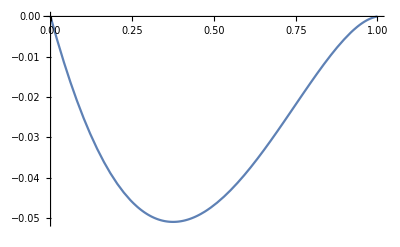

```mathematica
Plot[ϕfun[1,y],{y,0,1}]
```

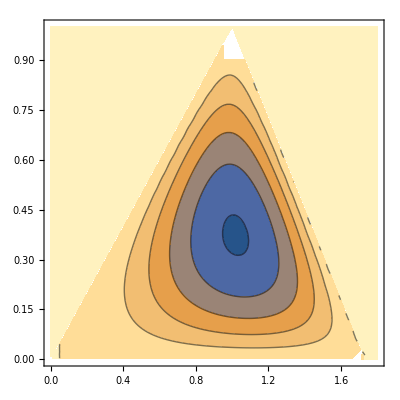

```mathematica
ContourPlot[ϕfun[x,y]Boole[y>0&&x>y&&x<xmax[y]],{x,0,1.8},{y,0,1},PlotPoints->40]
```